# Exercise 3.1

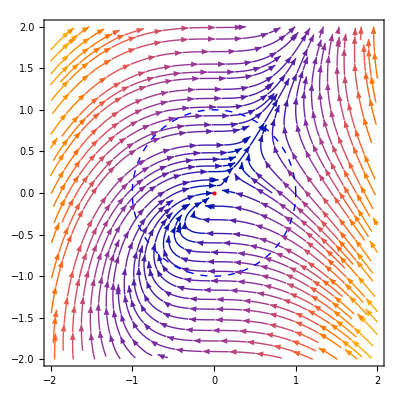

```mathematica
xdot[x_,y_]:=y-x
ydot[x_,y_]:=x^2

fp={{0,0}};

s =StreamPlot[{xdot[x,y],ydot[x,y]},{x,-2,2},{y,-2,2},StreamStyle->Darker[Blue],StreamPoints->Fine,Epilog->{Red,PointSize[Large],Point[fp]}];
c = ParametricPlot[{Cos[t], Sin[t]}, {t, 0, 2 Pi}, PlotStyle->{Dashed, Blue, Thick}];
Show[s,c]
```

Index = 0.

### Task b)

```mathematica
ClearAll["Global`*"]

x[r_,theta_] := r*Cos[θ]
y[r_,theta_] := r* Sin[θ]

xDot=D[x[r[t],θ[t]],t]
yDot=D[y[r[t],θ[t]],t]
```

Cos[θ] r'[t]

Sin[θ] r'[t]

```mathematica
(*
xDotSubst= Cos[θ]*(a*r+O[r^2]);
yDotSubst= Sin[θ]*(a*r+O[r^2]);
*)

(*For small r, O(r^2) is negligeble, and thus:*)
xDotFinal = Cos[θ]*a*r
xDotFinal = Sin[θ]*a*r

(*Which is just:*)
xDotCartesian[x_] = a*x
yDotCartesian[y_] = a*y
```

a r Cos[θ]

a r Sin[θ]

a x

a y

1

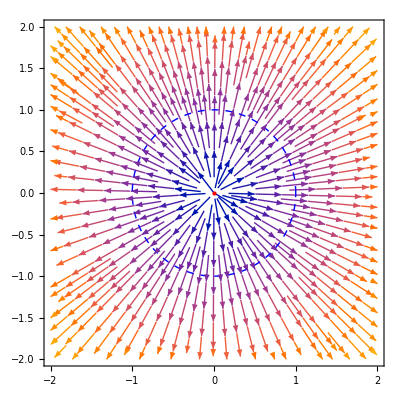

```mathematica
ClearAll["Global`*"]
(*Choose a != 0 and make streamplot, moreover we have an fp in {{0,0}}*)
a= 1
xdot[x_,y_] :=a*x
ydot[x_,y_] :=a*y
fp = {{0,0}};
s =StreamPlot[{xdot[x,y],ydot[x,y]},{x,-2,2},{y,-2,2},StreamStyle->Darker[Blue],StreamPoints->Fine,Epilog->{Red,PointSize[Large],Point[fp]}];

c = ParametricPlot[{Cos[t], Sin[t]}, {t, 0, 2 Pi}, PlotStyle->{Dashed, Blue, Thick}];
Show[s,c]
```

Index +1.

### task c)

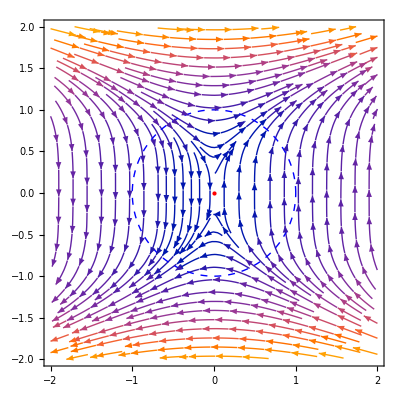

```mathematica
ClearAll["Global`*"]
xdot[x_,y_] := y^3
ydot[x_,y_] :=x

fp = {{0,0}};
s =StreamPlot[{xdot[x,y],ydot[x,y]},{x,-2,2},{y,-2,2},StreamStyle->Darker[Blue],StreamPoints->Fine,Epilog->{Red,PointSize[Large],Point[fp]}];

c = ParametricPlot[{Cos[t], Sin[t]}, {t, 0, 2 Pi}, PlotStyle->{Dashed, Blue, Thick}];
Show[s,c]
```

Index = -1

### Task d)

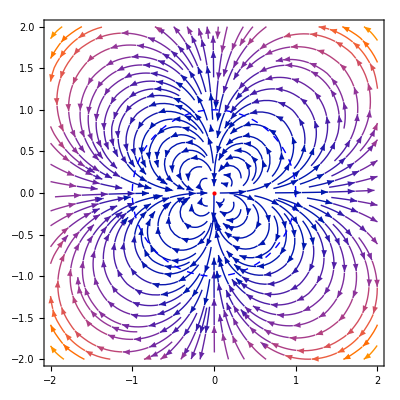

```mathematica
(*n != 0 integer, choose try different values and examine plot.*)
ClearAll["Global`*"]
n= 3;
xdot[x_,y_,n_] := (x^2+y^2)^(Abs[n]/2)*Cos[n*ArcTan[y/x]]
ydot[x_,y_,n_] := (x^2+y^2)^(Abs[n]/2)*Sin[n*ArcTan[y/x]]

fp = {{0,0}};
s =StreamPlot[{xdot[x,y,n],ydot[x,y,n]},{x,-2,2},{y,-2,2},StreamStyle->Darker[Blue],StreamPoints->Fine,Epilog->{Red,PointSize[Large],Point[fp]}];

c = ParametricPlot[{Cos[t], Sin[t]}, {t, 0, 2 Pi}, PlotStyle->{Dashed, Blue, Thick}];
Show[s,c]
```

After trying multiple values of n, the index seem to be the same as n, i.e when n = 1, index=1, etc. Thus index = n.